# ECE 533 HW2A Grant Ovsepyan Due 9/21/2022

1 a. Linear transformation of the image is the linear manipulation on the image, represented as a vector(set of vector)  or scalar that maps the pixel/numerical values to a different location. It is useful if you want to map the image into a different plane or warp it. The linear transformation should satisfy the following properties:
If T is a mapping function and u and v are vectors, while c is a scalar:
T(u +v)  = T(v) + T(u)
T(cu) = cT(u)

1 b. 3X is a linear transformation since 3 is a scalar:
T(c*X) = 3*cX= c*3X
___
T(x) = 3x
T(y) = 3y
T(x+y) = 3(x+y)= T(x) + t(y) = 3x + 3y

1 c. Median is not a linear transformation
if x = [1,2,3]. y = [9,3,1]. x+y = [10,4,4] => median of x+y is 4.
However the median(x) + median(y) = 2+3 = 5 which is not 4, thus median is not a linear transformation.

2 a ImageDimensions specifies the dimension image - the number of pixels that define height and width of an image . Dimensions of ImageData are the values of rgb converted to range 0 to 1, where the third dimensions specifies color, where pixels store the rgb values of color in form of a list for a given position.

```mathematica
R  = Import["rubberband.jpg"]
ImageDimensions[R]
```

-Graphics-

{640,480}

```mathematica
Dimensions[ImageData[R]]
```

{480,640,3}

```mathematica
ImageData[R]
```

2 b The dimensions of rescaled image are 426.667 by 320

```mathematica
H = ImageDimensions[R][[1]]*2/3;
W = ImageDimensions[R][[2]] *2/3;
NewR = ImageResize[R,{H,W}]
N[H]
N[W]
```

-Graphics-

426.667

320.

2 c The dimensions of the rescaled image are exactly the same as the dimensions of the original image (640 by 480).  The pixel values are identical as well. (ImageData[R]== ImageData[NewR evaluates as true).

```mathematica
H = H*3/2;
W = W*3/2;
NewR = ImageResize[R,{H,W}]
N[H]
N[W]
```

-Graphics-

640.

480.

```mathematica
ImageData[R]== ImageData[NewR]
```

True

2 d

```mathematica
GScale = ColorConvert[NewR,"Grayscale"]
```

-Graphics-

2 e. New size of the rotated image is 789 by 719.  Since the coordianate system did not rotate with the image, the image size increased.

```mathematica
Rotated =ImageRotate[GScale,27*Pi/180 ]
ImageDimensions[Rotated]
```

-Graphics-

{789,719}

2 f . size of doubly rotated image is 1030 by 999, which is bigger than the original image size ( 640 by 480). This is due to t he fact that created black margins upon first rotation are treated as a part of the new image, thus upon the linear rotation, they are also mapped into the new coordinates. the height between left upper corner and right corner defines the new height of doubly rotated image, which is why the size of the image increases

```mathematica
RotatedRight=ImageRotate[Rotated,-27*Pi/180 ]
ImageDimensions[RotatedRight]
```

-Graphics-

{1030,999}

3 a .

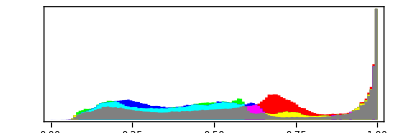

```mathematica
Hist  = ImageHistogram[R]
```

3 b .

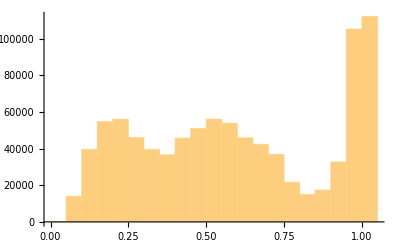

```mathematica
Histogram[Flatten[ImageData[R]]]
```

3 c .

```mathematica
Histogram3D[Flatten[ImageData[R][[All, All, {1, 2}]],1]]
```

-Graphics3D-

ImageHistogram shows the histogram of red, green and blue channels of the image. It is useful in case when  user desires to adjust the color of the image, change contrast of the image
Histogram shows the frequency of the values between 0 and 1. It might be useful for evaluating the greyscale image and fine-tuning the brightness of the greyscale image
Histogram3D shows the histogram of the values {xi,yi}. It is useful whenever the user works with 2D images/objects with dimensions, where the third value is represented as the z axis